## Pulse Width Modulation Principle

```mathematica
Manipulate[
Plot[{((Sin[x]*m)+(Sin[x*3]*1/3*d)),If[x<π,1,-1]*If[s,1,0]*(2.5*Abs[Round[(c/2*x)/π]-(c/2*x)/π]),If[x<π,If[((Sin[x]*m)+(Sin[x*3]*1/3*d))≥(2.5*Abs[Round[(c/2*x)/π]-(c/2*x)/π]),1.25,0],If[((Sin[x]*m)+(Sin[x*3]*1/3*d))≤(-2.5*Abs[Round[(c/2*x)/π]-(c/2*x)/π]),-1.25,0]]},{x,0,2π},
PlotStyle->{{RGBColor[0.7,0.9,0.3],Thickness[0.005]},
{RGBColor[0.1,0.33,1],Thickness[0.002]},
{RGBColor[1,0.33,0.1],Thickness[0.002]}},
AxesLabel->{"time",
"voltage"
},
PlotPoints->500,
AxesOrigin->{0,0},
PlotRange->{-1.4,1.4},
PlotLabel->Style["pulse width modulation",14],
Filling->{1->Axis,3->Axis},
FillingStyle->Automatic,
PerformanceGoal->"Quality",
ImageSize->{550, 390}
],
{{c,24,"relative carrier frequency" },{12,24,48},
ControlType->SetterBar},
{{s,True,"show carrier triangle signal"},{True,False}},
{{m,1,"reference magnitude (-60% +20%)"},
0.4,1.2,Appearance->"Labeled"},
{{d,0,"reference distortion"},
0,1,Appearance->"Labeled"},
TrackedSymbols:>Manipulate
]
```

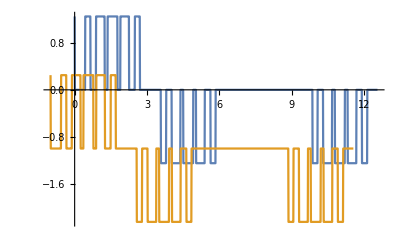

```mathematica
ClearAll;

c=12;m=1;d=0;
s=True;ff[x_]=If[x<π,If[((Sin[x]*m)+(Sin[x*3]*1/3*d))≥(2.5*Abs[Round[(c/2*x)/π]-(c/2*x)/π]),1.25,0],If[((Sin[x]*m)+(Sin[x*3]*1/3*d))≤(-2.5*Abs[Round[(c/2*x)/π]-(c/2*x)/π]),-1.25,0]];
aaa=Table[
{
x,ff[x]
},{x,0,4π,0.01}];
ListPlot[
{aaa,aaa-1},PlotLegends->"Expressions",Joined->True]
```